#### define variables

```mathematica
xc = 0;
yc = 0;
ptc = {xc,yc};
ptmax = {xmax, ymax};
npts = 10;
ri = 1;
kg = 2.1;
rg = ri *kg;
sunnyshady = Sin[0.3x]Sin[0.5y];
initialcircle = CirclePoints[ri, 10];
```

```mathematica
exGrad=Grad[funcSunnyShady[x,y],{x,y}]
```

{0.3 Cos[0.3 x] Sin[0.5 y],0.5 Cos[0.5 y] Sin[0.3 x]}

```mathematica
exGrad/.{x->initialcircle[[1,1]],y->initialcircle[[1,2]]}
```

{-0.136753,0.0411508}

```mathematica
exGrad/.{x->initialcircle[[All,1]],y->initialcircle[[All,2]]}
```

{{-0.136753,-0.084357,0.,0.084357,0.136753,0.136753,0.084357,0.,-0.084357,-0.136753},{0.0411508,0.115012,0.14776,0.115012,0.0411508,-0.0411508,-0.115012,-0.14776,-0.115012,-0.0411508}}

#### define functions to use

```mathematica
funcSunnyShady[x_,y_]:=Sin[.3x]Sin[.5y]
```

```mathematica
findGradPoints[scalarFunc_,circlePoints_,x_,y_]:=
Transpose[Grad[scalarFunc[x,y],{x,y}]/.{x->circlePoints[[All,1]],y->circlePoints[[All,2]]}]
```

findGradPoints is now a transpose so it yields a list like {{x1,y1},{x2,y2},...,{xn,yn}} rather than {{x1,x1,...,xn},{y1,y2,...,yn}}

```mathematica
findMaxPoint[listCirclePoints_,listGradPoints_]:=Partition[Flatten[listCirclePoints[[#]]&/@Position[Norm/@listGradPoints,Max[Norm/@listGradPoints]]],2]
```

So, findMaxPoint. This is a thing. Norm/@listGradPoints turns listGradPoints from a list of points to a list of magnitudes.
Position[listMags, Max[listMags]] finds the position(s) of the max of the list.
listCirclePoints[[#]]&/@Position yields a list of the position(s) of max of the list.
Partition[Flatten[positionsList],2] makes the lists not Super Nested, like {{{1,0}},{{-1,0}}} to {{1,0},{-1,0}}

#### find the point on boundary of circle with maximum gradient

```mathematica
listPoints=findGradPoints[funcSunnyShady,initialcircle,x,y]
```

{{-0.136753,0.0411508},{-0.084357,0.115012},{0.,0.14776},{0.084357,0.115012},{0.136753,0.0411508},{0.136753,-0.0411508},{0.084357,-0.115012},{0.,-0.14776},{-0.084357,-0.115012},{-0.136753,-0.0411508}}

```mathematica
findMaxPoint[initialcircle,listPoints]
```

{{1,0},{-1,0}}

#### draw things

```mathematica
p0 = Graphics[initialcircle]
```

-Graphics-

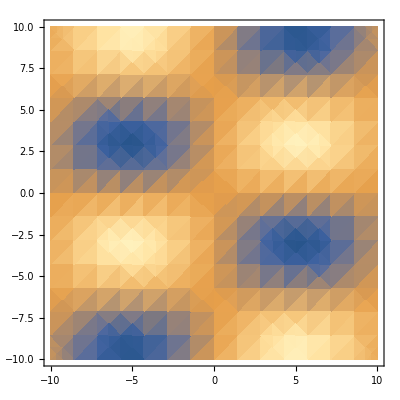

```mathematica
p1 = DensityPlot[Sin[0.3x]Sin[0.5y],{x,-10,10},{y,-10,10}]
```

```mathematica
Show[p1,p0]
```

-Graphics-